# Hyperspherical Package

Hyperspherical Tree Graphspaclet:Hyperspherical/tutorial/HypersphericalPackage#164608979 | Multivariable Calculuspaclet:Hyperspherical/tutorial/HypersphericalPackage#686880320
Coordinate System Propertiespaclet:Hyperspherical/tutorial/HypersphericalPackage#148900360 | Hyperspherical Harmonics (Eigenfunctions of the Hyperangular Laplacian)paclet:Hyperspherical/tutorial/HypersphericalPackage#9772947

This package is roughly a translation into the Wolfram Language of Chapter 6 of Classical Orthogonal Polynomials of a Discrete Variable by Arnold F. Nikiforov, Sergei K. Suslov, Vasilii B. Uvarov.

The functions defined in the Hyperspherical` context provide support for hyperspherical tree graphs in order to define non-canonical hyperspherical coordinate systems. These naturally lead to the hyperspherical harmonic functions.

This loads the package:

```mathematica
<<Hyperspherical`
```

## Hyperspherical Tree Graphs

The hyperspherical tree graph is a binary tree graph with d_ leaves (degrees of freedom), but the order of the branches matters. The graph is directed from the root to the leaves. These graphs are a representation of the decomposition of a space into the direct sum of orthogonal subspaces.

### Canonical

HypersphericalTreeGraph[d_] | create a canonical hyperspherical tree graph with d_ leaves

Creating canonical hyperspherical trees.

The two- and three-dimensional canonical hyperspherical tree graphs.

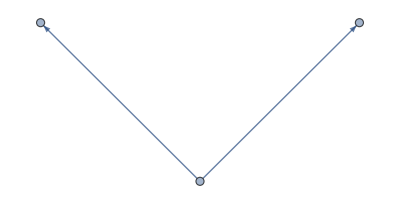

```mathematica
HypersphericalTreeGraph[2]
```

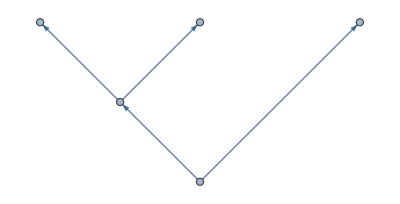

```mathematica
HypersphericalTreeGraph[3]
```

None | (default) no labels
Automatic | labels are iL[_], iR[_], and iRoot[_]
"Angles" | display the hyper angles at each branch
"Ordering" | display the index order of the branches

Option values for VertexLabels.

The fixed order is encoded in the graphs using the inert vertex wrappers iLpaclet:Hyperspherical/ref/iL, iRpaclet:Hyperspherical/ref/iR, and iRootpaclet:Hyperspherical/ref/iRoot.

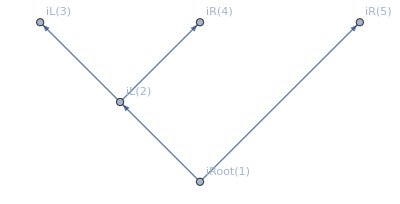

```mathematica
HypersphericalTreeGraph[3,VertexLabels→Automatic]
```

The graphical method for converting from Cartesian to hyperspherical coordinates is to follow the path from the root to the leaf. Every branch that goes to the left is a factor of Sin of the hyper angle, while every branch that goes to the right is a factor of Cos of the hyper angle. A factor of the hyper radius R is also included.

Polar and spherical coordinates are special cases of the more general d_-dimensional trees.

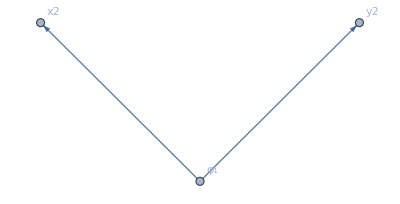

```mathematica
g2=HypersphericalTreeGraph[2,VertexLabels->"Angles"];
PropertyValue[{g2,iL[2]},VertexLabels]="x2";
PropertyValue[{g2,iR[3]},VertexLabels]="y2";
g2
```

```mathematica
x2=R Sin[Subscript[ϕ, 1]];
y2=R Cos[Subscript[ϕ, 1]];
```

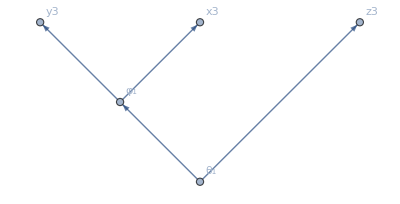

```mathematica
g3=HypersphericalTreeGraph[3,VertexLabels->"Angles"];
PropertyValue[{g3,iL[3]},VertexLabels]="y3";
PropertyValue[{g3,iR[4]},VertexLabels]="x3";
PropertyValue[{g3,iR[5]},VertexLabels]="z3";
g3
```

```mathematica
x3=R Sin[Subscript[θ, 1]] Cos[Subscript[ϕ, 1]];
y3=R Sin[Subscript[θ, 1]] Sin[Subscript[ϕ, 1]];
z3=R Cos[Subscript[θ, 1]];
```

The ordering of branches is determined by starting at the root and moving towards the left-most branch. The next path again starts at the root, but moves to the second left-most branch. This method is continued until the path is defined that reaches the right-most branch. Vertices are only enumerated once.

Canonical trees have a straightforward enumeration of branch paths.

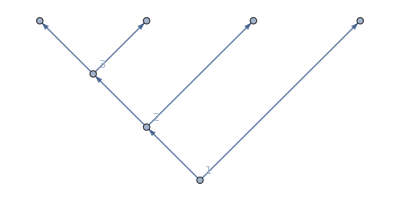

```mathematica
HypersphericalTreeGraph[4,VertexLabels->"Ordering"]
```

### Non-canonical

A high-level input syntax can be used to create hyperspherical tree graphs of any shape.

HypersphericalTreeGraph[{b_1, b_2, …] | creates a hyperspherical tree graph with the branching edges b_j

General hyperspherical tree graphs.

To indicate left versus right, a branching edge b_j is a rule that goes to a list of two elements. The first element indicates left and the second element indicates right. If a graph is used, then it appears as a head with a single argument that acts as a unique label.

The branching edge takes one of the following forms:

v_1 → {v_2, v_3} | Vertex v_1 points left to vertex v_2 and right to vertex v_3.
v_1 → {v_2, g[1]} | Vertex v_1 points left to vertex v_2 and right to the root of hyperspherical tree graph g[1].
v_1 → {g[1], v_2} | Vertex v_1 points left to the root of hyperspherical tree graph g[1] and right to vertex v_2.
v_1 → {g[1], g[2]} | Vertex v_1 points left to the root of hyperspherical tree graph g[1] and right to to the root of hyperspherical tree graph g[2].
g[1,n] → {_, _} | The nth leaf of hyperspherical tree graph g[1] branches like in the above examples.

Normal branching rules.

Larger hyperspherical tree graphs can be constructed using standard branching rules.

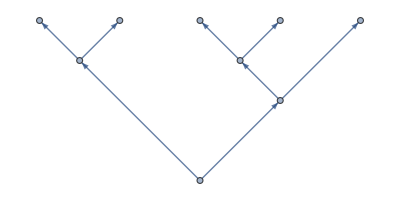

```mathematica
HypersphericalTreeGraph[{1->{2,3},2->{4,5},3->{6,7},6->{8,9}}]
```

It is often easier to use smaller graph forms to construct larger graphs. The label 'A' can be used twice because graphs g2 and g3 have different structure.

```mathematica
g5=HypersphericalTreeGraph[{1->{g2[A],g3[A]}}]
```

-Graphics-

A branching edge b_j can also take one of the following special forms:

v_1 → g[1] | Vertex v_1 is replaced by the hyperspherical tree graph of the form g[1], where the root of g[1] is in place of v_1. 
g[1,n] → g[2] | The nth leaf of hyperspherical tree graph g[1] becomes the root of a hyperspherical tree graph of the form g[2].
g[1] → g[2] | All leaves of hyperspherical tree graph g[1] becomes the root of a hyperspherical tree graph of the form g[2].

Special branching rules where a vertex is replaced by a larger structure.

Structures can be built up quickly using the special branching rules.

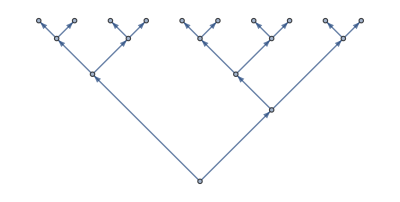

```mathematica
HypersphericalTreeGraph[{g5[A]->g2[B]}]
```

For busier graphs, suppressing the edge arrows helps readability.

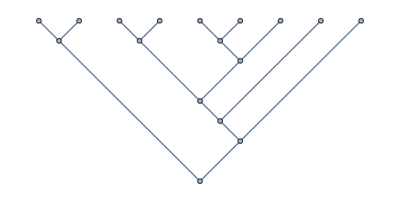

```mathematica
HypersphericalTreeGraph[{g5[A,3]->g5[B]},EdgeShapeFunction->"Line"]
```

Using a graph to replace its own leaves leads to a fractal-like tree.

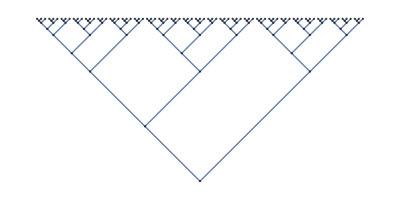

```mathematica
Nest[HypersphericalTreeGraph[{#[1]->g3[2]},EdgeShapeFunction->"Line"]&,g3,3]
```

### Number of "Skeleton Graphs" for d Degrees of Freedom

The number of unique trees for fixed number of leaves is given by the Catalan numbers. As a numerical demonstration, we can start with the unique two leaf graph and recursively branch all of the leaves to make all possible three-leaf graphs, then repeat.

To make sure we remove identical tree structures, we use the function HypersphericalTreeSameQpaclet:Hyperspherical/ref/HypersphericalTreeSameQ.

HypersphericalTreeSameQ[g$1,g$2] | tests for identical hyperspherical tree structures

A useful test for hyperspherical tree similarity.

All three-leaf trees

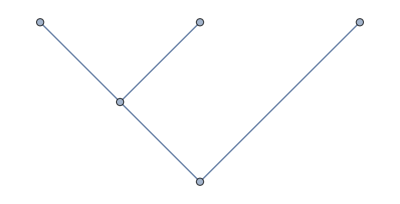
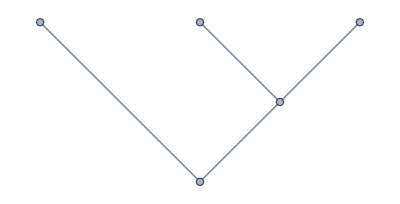

```mathematica
A3=HypersphericalTreeGraph[{g2[1,#]->g2[2]},EdgeShapeFunction->"Line",ImageSize->Tiny]&/@Range[2]
```

All 4-leaf trees

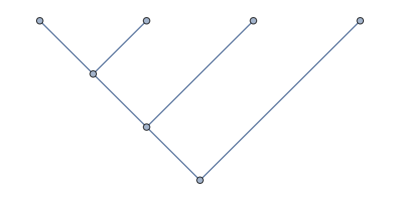
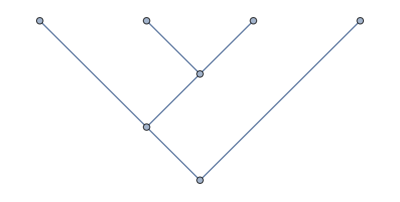
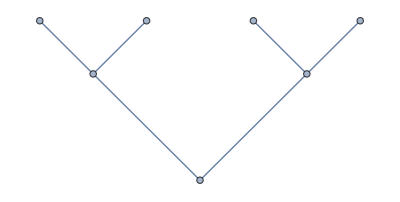
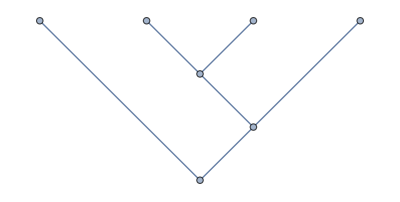
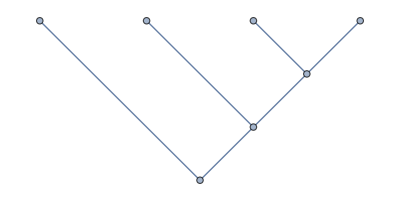

```mathematica
A4=DeleteDuplicates[Join@@Table[HypersphericalTreeGraph[{i[1,#]->g2[2]},EdgeShapeFunction->"Line",ImageSize->Tiny]&/@Range[3],{i,A3}],HypersphericalTreeSameQ]
```

All 5-leaf trees

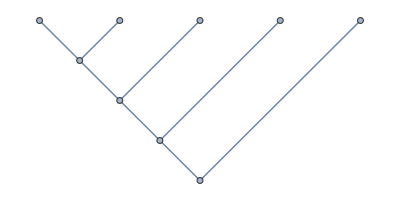
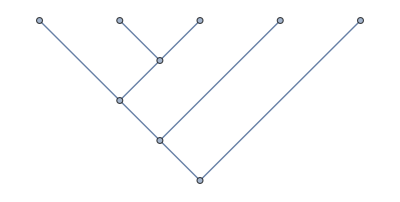
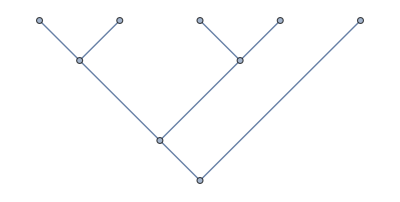
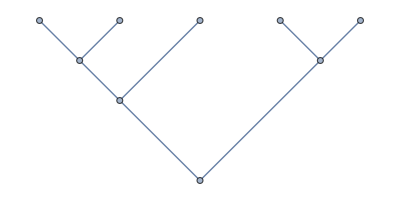
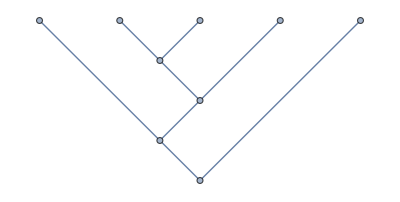
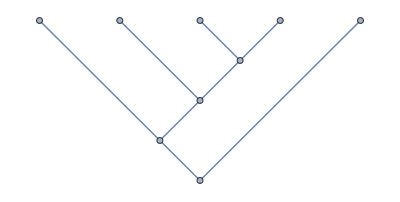
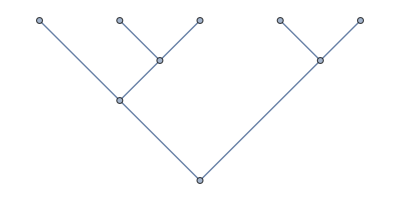
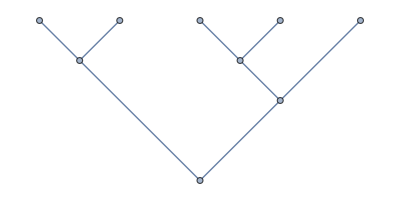

```mathematica
A5=DeleteDuplicates[Flatten[Table[HypersphericalTreeGraph[{i[1,#]->g2[2]},EdgeShapeFunction->"Line",ImageSize->Tiny]&/@Range[4],{i,A4}],1],HypersphericalTreeSameQ]
```

All 6-leaf trees

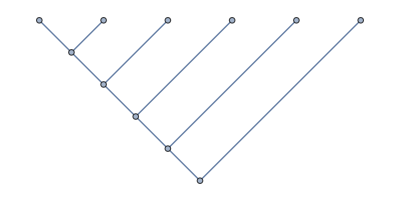
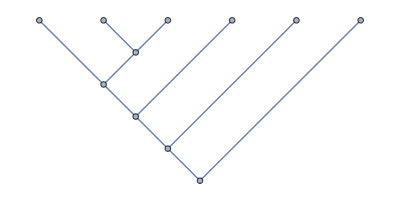
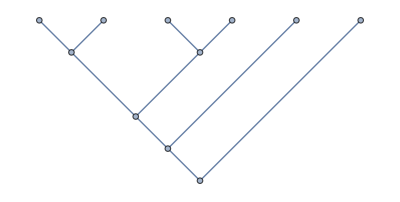
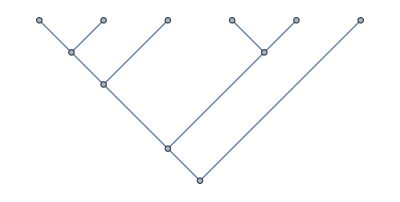
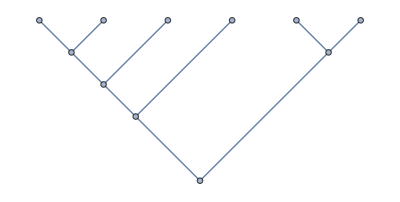
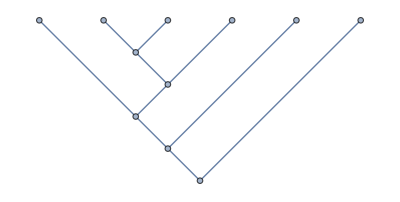
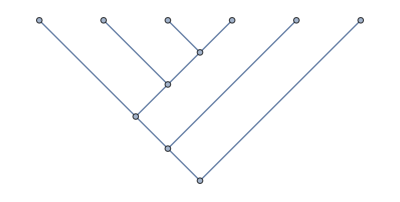
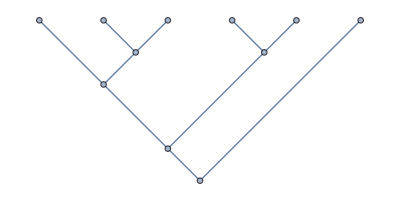

```mathematica
A6=DeleteDuplicates[Flatten[Table[HypersphericalTreeGraph[{i[1,#]->g2[2]},EdgeShapeFunction->"Line",ImageSize->Tiny]&/@Range[5],{i,A5}],1],HypersphericalTreeSameQ]
```

The number of trees at each step

```mathematica
Length/@{A3,A4,A5,A6}
```

{2,5,14,42}

```mathematica
CatalanNumber/@Range[5]
```

{1,2,5,14,42}

## Coordinate System Properties

Hyperspherical tree graphs are incorporated into CoordinateChartData to allow quick access to the underlying coordinate system properties.

CoordinateChartData[{"Hyperspherical","Euclidean",g_},"Properties"] | syntax to use CoordinateChartData with hyperspherical tree graphs

Overloading of existing syntax.

### Standard Coordinate Names

Properties like the standard coordinate names are used when using VertexLabels → "Angles".

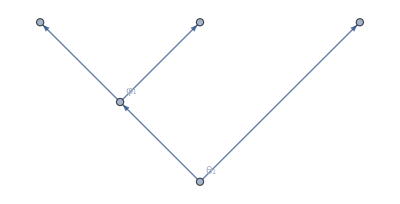

```mathematica
g3=HypersphericalTreeGraph[3,VertexLabels->"Angles"]
```

```mathematica
CoordinateChartData[{"Hyperspherical","Euclidean",g3},"StandardCoordinateNames"]
```

{R,θ_1,φ_1}

### Coordinate Ranges

The variables have particular ranges depending on the branch structure. Note the difference between θ and θ̄.

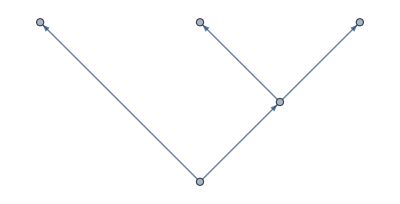

```mathematica
g3a=HypersphericalTreeGraph[{g2[A,2]->g2[B]}]
```

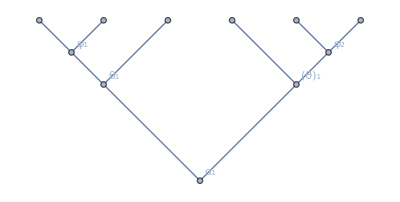

```mathematica
g6=HypersphericalTreeGraph[{g2[A]->{g3[A],g3a[A]}},EdgeShapeFunction->"Line",VertexLabels->"Angles"]
```

```mathematica
g6coords=CoordinateChartData[{"Hyperspherical","Euclidean",g6},"StandardCoordinateNames"]
```

{R,α_1,θ_1,φ_1,(θ̄)_1,φ_2}

```mathematica
CoordinateChartData[{"Hyperspherical","Euclidean",g6},"CoordinateRangeAssumptions",%]
```

0<R&&0<α_1<π/2&&0<θ_1<π&&0<φ_1<2 π&&-π/2<(θ̄)_1<π/2&&0<φ_2<2 π

### Volume Element

The volume element is needed to compute integrals over the unit hypersphere.

Using g6 above as an example.

```mathematica
CoordinateChartData[{"Hyperspherical","Euclidean",g6},"VolumeFactor",g6coords]
```

R^5 Cos[α_1]^2 Cos[(θ̄)_1] Sin[α_1]^2 Sin[θ_1]

## Multivariable Calculus

Functions like Grad, Div, Curl, and Laplacian also accept hyperspherical tree graphs to define hyperspherical coordinate systems.

### Grad

Defining a symmetric tree with 4 degrees of freedom.

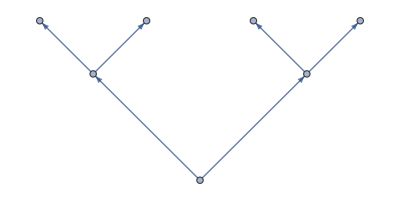

```mathematica
g4=HypersphericalTreeGraph[{g2[A]->{g2[B],g2[C]}}]
```

```mathematica
var4=CoordinateChartData[{"Hyperspherical","Euclidean",g4},"StandardCoordinateNames"]/.x_String:>ToExpression[x]
```

{R,α_1,φ_1,φ_2}

```mathematica
Clear[x1,x2,x3,x4];
Grad[f@@var4,var4,{"Hyperspherical","Euclidean",g4}]
```

{f^(1,0,0,0)[R,α_1,φ_1,φ_2],(f^(0,1,0,0)[R,α_1,φ_1,φ_2])/R,(Csc[α_1] f^(0,0,1,0)[R,α_1,φ_1,φ_2])/R,(Sec[α_1] f^(0,0,0,1)[R,α_1,φ_1,φ_2])/R}

### Div

Symbolic

```mathematica
Div[{f1@@var4,f2@@var4,f3@@var4,f4@@var4},var4,{"Hyperspherical","Euclidean",g4}]
```

(Sec[α_1] (Cos[α_1] f1[R,α_1,φ_1,φ_2]-f2[R,α_1,φ_1,φ_2] Sin[α_1]+f4^(0,0,0,1)[R,α_1,φ_1,φ_2]))/R+1/R Csc[α_1] (Cos[α_1] f2[R,α_1,φ_1,φ_2]+f1[R,α_1,φ_1,φ_2] Sin[α_1]+f3^(0,0,1,0)[R,α_1,φ_1,φ_2])+(f1[R,α_1,φ_1,φ_2]+f2^(0,1,0,0)[R,α_1,φ_1,φ_2])/R+f1^(1,0,0,0)[R,α_1,φ_1,φ_2]

### Curl

Symbolic

```mathematica
Curl[{f1@@var4,f2@@var4,f3@@var4,f4@@var4},var4,{"Hyperspherical","Euclidean",g4}]
```

StructuredArray[SymmetrizedArray, {4, 4}, <6,Antisymmetric[{1, 2}]>]

### Laplacian

Symbolic

```mathematica
Laplacian[f@@var4,var4,{"Hyperspherical","Euclidean",g4}]//Simplify
```

1/R^2(Sec[α_1]^2 f^(0,0,0,2)[R,α_1,φ_1,φ_2]+Csc[α_1]^2 f^(0,0,2,0)[R,α_1,φ_1,φ_2]+Cot[α_1] f^(0,1,0,0)[R,α_1,φ_1,φ_2]-Tan[α_1] f^(0,1,0,0)[R,α_1,φ_1,φ_2]+f^(0,2,0,0)[R,α_1,φ_1,φ_2]+3 R f^(1,0,0,0)[R,α_1,φ_1,φ_2]+R^2 f^(2,0,0,0)[R,α_1,φ_1,φ_2])

## Hyperspherical Harmonics (Eigenfunctions of the Hyperangular Laplacian)

As the SphericalHarmonicY functions are the eigenfunctions of the three-dimensional Laplacian operator in spherical coordinates, so is the HypersphericalHarmonicYpaclet:Hyperspherical/ref/HypersphericalHarmonicY functions in higher dimensions.

### Functional Form

In polar coordinates solution is a complex exponential.

```mathematica
HypersphericalHarmonicY[{m},{ϕ},g2]
```

ⅇ^(ⅈ m ϕ)/(√(2 π))

In spherical coordinates, HypersphericalHarmonicYpaclet:Hyperspherical/ref/HypersphericalHarmonicY reduces to the SphericalHarmonicY function within a factor of -1.

```mathematica
g3
```

-Graphics-

```mathematica
SphericalHarmonicY[4,-1,Subscript[θ, 1],Subscript[φ, 1]]/HypersphericalHarmonicY[{4,-1},{Subscript[θ, 1],Subscript[φ, 1]},g3]//Simplify
```

1

The inverted 3-D system resembles the standard 3-D system, but with a shift of coordinates.

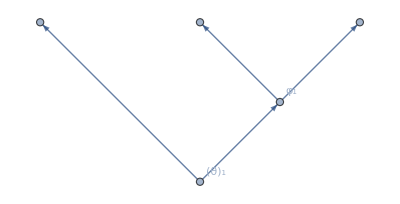

```mathematica
HypersphericalTreeGraph[g3a,VertexLabels->"Angles"]
```

```mathematica
SphericalHarmonicY[4,-1,π/2-Subscript[θ, 1],Subscript[φ, 1]]/HypersphericalHarmonicY[{4,-1},{Subscript[θ, 1],Subscript[φ, 1]},g3a]//FullSimplify
```

1

### Angular Momenta Restrictions

The momenta can take on integer values. The hierarchy of angular momentum addition puts constraints on their values. The symbolic evaluation shows these constraints in the conditional statements.

Recall our graph g5

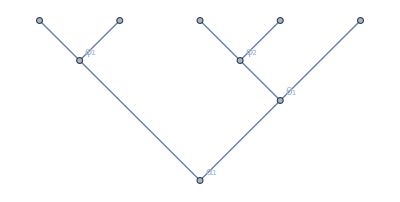

```mathematica
HypersphericalTreeGraph[g5,VertexLabels->"Angles",EdgeShapeFunction->"Line"]
```

```mathematica
HypersphericalHarmonicY[{λ1,m1,L,m2},{α1,ϕ1,θ1,ϕ2},g5][[2]]
```

m2∈Integers&&(λ1|m1|L)∈Integers&&(-1)^λ1==(-1)^(L+Abs[m1])&&L≥Abs[m2]&&λ1≥L+Abs[m1]

If the constraints are violated, then the function returns 0.

This passes all constraints.

```mathematica
HypersphericalHarmonicY[{5,-4,1,-1},{α1,ϕ1,θ1,ϕ2},g5]
```

(3 √(5005/2) ⅇ^(-4 ⅈ ϕ1-ⅈ ϕ2) Cos[α1] Sin[α1]^4 Sin[θ1])/(32 π)

This fails the constraint 5 ≥ 2 + |-4|.

```mathematica
HypersphericalHarmonicY[{5,-4,2,-1},{α1,ϕ1,θ1,ϕ2},g5]
```

0

This fails the constraint (-1)^5==(-1)^(-3+1).

```mathematica
HypersphericalHarmonicY[{5,-3,1,-1},{α1,ϕ1,θ1,ϕ2},g5]
```

0

### Eigenvalues

The eigenvalues are given by λ(λ+d-2) where λ is the first angular momentum value in the list of angular momenta. This is known as the grand angular momentum.

An example with 5 degrees of freedom.

```mathematica
HypersphericalTreeGraph[g5,VertexLabels->"Angles",EdgeShapeFunction->"Line"]
```

-Graphics-

```mathematica
state=HypersphericalHarmonicY[{5,-4,1,-1},{α1,ϕ1,θ1,ϕ2},g5]
```

(3 √(5005/2) ⅇ^(-4 ⅈ ϕ1-ⅈ ϕ2) Cos[α1] Sin[α1]^4 Sin[θ1])/(32 π)

```mathematica
Laplacian[state,{R,α1,ϕ1,θ1,ϕ2},{"Hyperspherical","Euclidean",g5}]/state==(-5 (5+5-2))/R^2//Simplify
```

True

### The Number of Hyperspherical Harmonics for a Fixed λ and Dimensionality

There is a known formula for the number of states at a fixed grand angular momentum λ.

Dimension is set at 'd'.

```mathematica
degen[λ_,d_]:=((2 λ+d-2) Gamma[λ+d-2])/(Gamma[λ+1] Gamma[d-1])
```

The spherical harmonics have a degeneracy of 2L+1, where L is the grand angular momentum in three dimensions.

```mathematica
degen[L,3]
```

1+2 L

The number of states at a fixed λ is independent of coordinate system, as it should be.

Brute force enumeration for λ=3, d=4 and tree structure

```mathematica
g4
```

-Graphics-

```mathematica
Cases[Flatten[Table[{{3,λ2,λ3},HypersphericalHarmonicY[{3,λ2,λ3},{a,b,c},g4]},{λ2,-3,3,1},{λ3,-3,3,1}],1],{_,Except[0]}][[All,1]]
```

{{3,-3,0},{3,-2,-1},{3,-2,1},{3,-1,-2},{3,-1,0},{3,-1,2},{3,0,-3},{3,0,-1},{3,0,1},{3,0,3},{3,1,-2},{3,1,0},{3,1,2},{3,2,-1},{3,2,1},{3,3,0}}

```mathematica
Length[%]
```

16

```mathematica
degen[3,4]
```

16

Brute force enumeration for λ=3, d=4 and tree structure

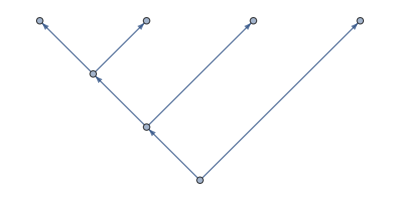

```mathematica
g4a=HypersphericalTreeGraph[4]
```

```mathematica
Cases[Flatten[Table[{{3,λ2,λ3},HypersphericalHarmonicY[{3,λ2,λ3},{a,b,c},g4a]},{λ2,-3,3,1},{λ3,-3,3,1}],1],{_,Except[0]}][[All,1]]
```

{{3,0,0},{3,1,-1},{3,1,0},{3,1,1},{3,2,-2},{3,2,-1},{3,2,0},{3,2,1},{3,2,2},{3,3,-3},{3,3,-2},{3,3,-1},{3,3,0},{3,3,1},{3,3,2},{3,3,3}}

```mathematica
Length[%]
```

16

```mathematica
degen[3,4]
```

16

### Orthogonality

Each state is orthonormal when integrated with respect to the unit hypersphere.

Looking at states {3,0,0} and {3,1,-1} from the last example.

```mathematica
vars=CoordinateChartData[{"Hyperspherical","Euclidean",g4a},"StandardCoordinateNames"]/.x_String:>ToExpression[x]
```

{R,θ_1,θ_2,φ_1}

```mathematica
vol=CoordinateChartData[{"Hyperspherical","Euclidean",g4a},"VolumeFactor",vars]/.R->1
```

Sin[θ_1]^2 Sin[θ_2]

```mathematica
ranges=Sequence@@Rest[CoordinateChartData[{"Hyperspherical","Euclidean",g4a},"CoordinateRangeAssumptions",vars]/.Less[a_,b_,c_]:>{b,a,c}]
```

Sequence[{θ_1,0,π},{θ_2,0,π},{φ_1,0,2 π}]

```mathematica
state1=HypersphericalHarmonicY[{3,0,0},Rest[vars],g4a];
state2=HypersphericalHarmonicY[{3,1,-1},Rest[vars],g4a];
```

Checking the normalization of state1

```mathematica
Integrate[(state1/.x_Complex:>Conjugate[x])*state1*vol,ranges]
```

1

Checking the orthogonality of state1 and state2.

```mathematica
Integrate[(state1/.x_Complex:>Conjugate[x])*state2*vol,ranges]
```

0